## Basic Evolution

Basic evolution:

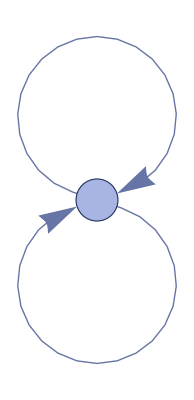
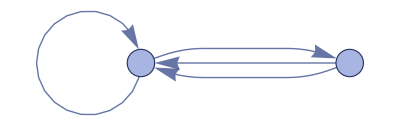
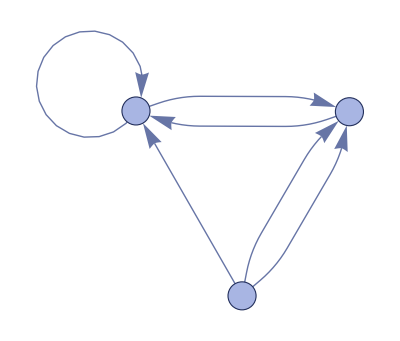
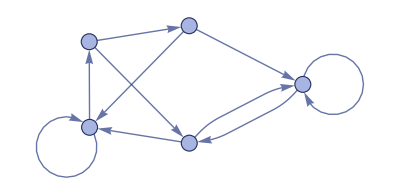
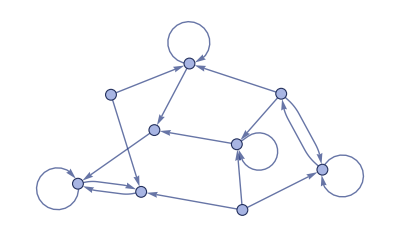
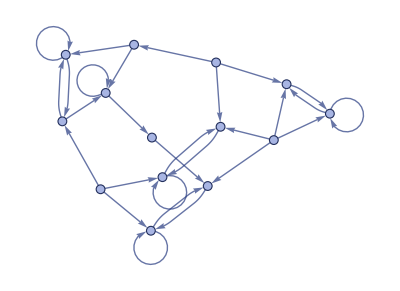
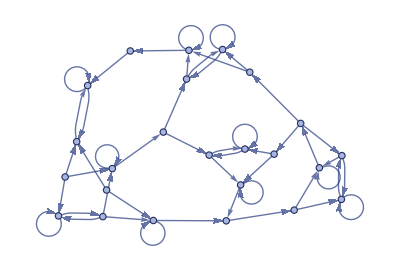

```mathematica
[{{{1,2},{2,3}}->{{4,4},{4,1},{2,4},{3,4}}},{{1,1},{1,1}},6,"StatesPlotsList"]
```

Event-by-event evolution:

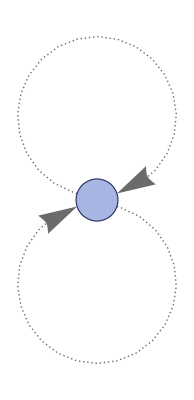
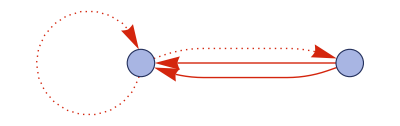
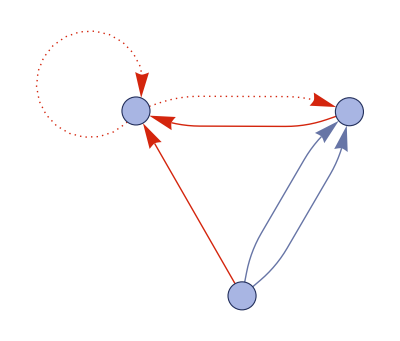
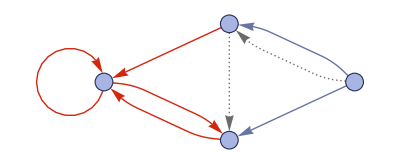
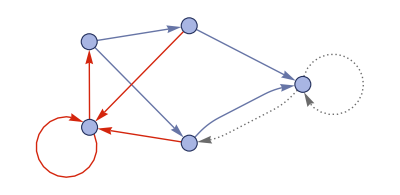
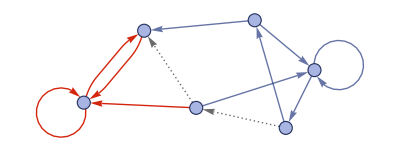
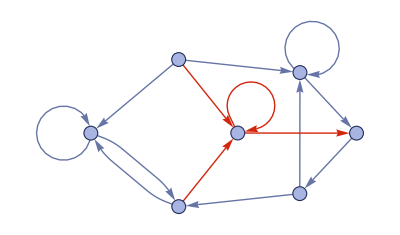

```mathematica
[{{{1,2},{2,3}}->{{4,4},{4,1},{2,4},{3,4}}},{{1,1},{1,1}},<|"MaxEvents"->6|>,"EventsStatesPlotsList"]
```

Vertex and edge counts:

```mathematica
{vertexCountList,edgeCountList}=[{{{1,2},{2,3}}->{{4,4},{4,1},{2,4},{3,4}}},{{1,1},{1,1}},16,{"VertexCountList","EdgeCountList"}];
```

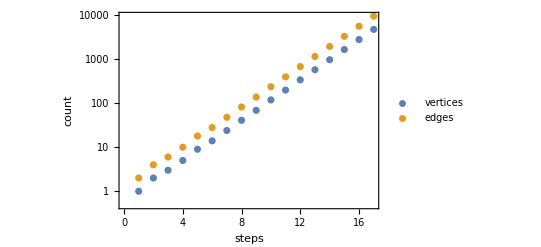

```mathematica
ListLogPlot[{vertexCountList,edgeCountList},]
```

Result after 8 generations:

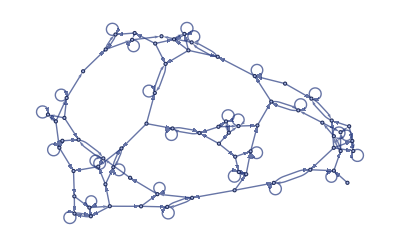

```mathematica
["FinalStatePlot"]
```

## Causal Graph

Causal graph:

```mathematica
["CausalGraph",]
```

-Graphics-

Layered rendering:

```mathematica
["LayeredCausalGraph"]
```

-Graphics-

Causal graph distance matrix:

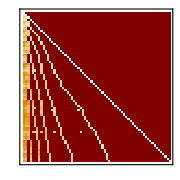

```mathematica
MatrixPlot[Transpose[GraphDistanceMatrix[["CausalGraph"]]],]
```

## Final State Properties

Hypergraph adjacency matrix:

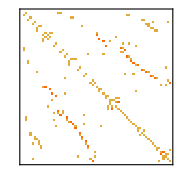

```mathematica
MatrixPlot[AdjacencyMatrix@Catenate[Map[UndirectedEdge@@@Subsets[#,{2}]&,["FinalState"]]],]
```

Vertex degree distribution:

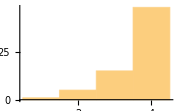

```mathematica
Histogram[Values[Counts[Catenate[Union/@["FinalState"]]]],]
```

Neighborhood volumes (ignoring directedness of connections):

```mathematica
volumes=[Values[[["FinalState"],All,Automatic]]];
```

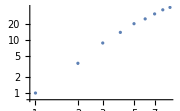

```mathematica
ListLogLogPlot[volumes,]
```

Effective dimension versus radius:

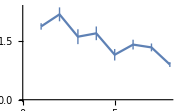

```mathematica
ListLinePlot[[volumes],]
```

Successive neighborhood balls around a random vertex:

```mathematica
[["FinalState"],4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Distance matrix:

```mathematica
distanceMatrix=GraphDistanceMatrix[UndirectedGraph[[["FinalState"]]]];
```

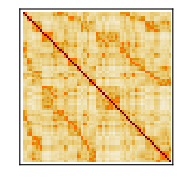

```mathematica
MatrixPlot[Exp[-(distanceMatrix/. 0->None)],]
```

Distribution of distances in the graph:

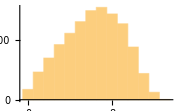

```mathematica
Histogram[Flatten[distanceMatrix],]
```

## Spreading of Effects

Causal graph adjacency matrix:

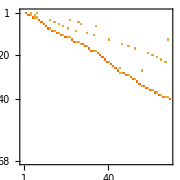

```mathematica
MatrixPlot[AdjacencyMatrix[["CausalGraph"]],]
```

Neighborhood volumes in causal graph:

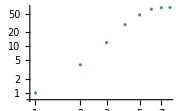

```mathematica
ListLogLogPlot[Values[[["CausalGraph"],{1}]],]
```

## Other Evolution Orders

Random evolutions:

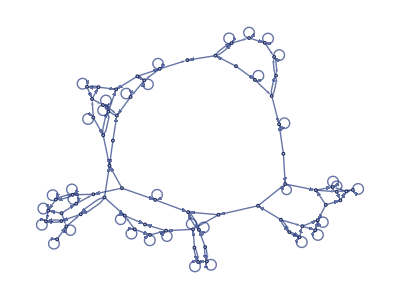

```mathematica
[{{{1,2},{2,3}}->{{4,4},{4,1},{2,4},{3,4}}},{{1,1},{1,1}},<|"MaxEvents"->68|>,"FinalStatePlot","EventOrderingFunction"->"Random"]
```

Different deterministic evolution orders:

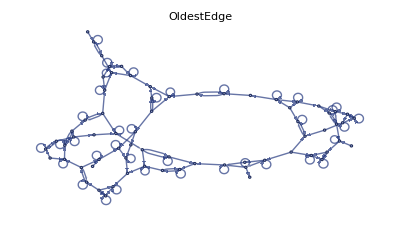
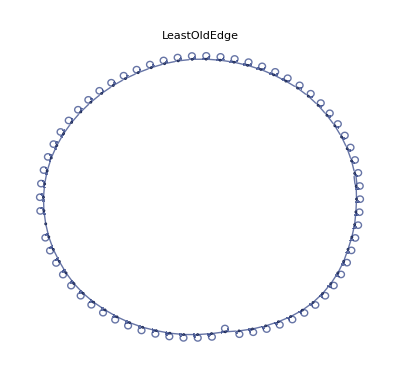
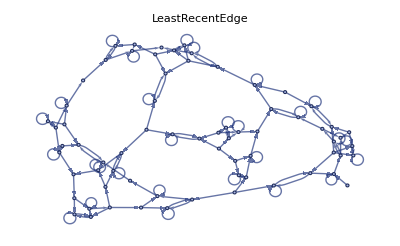
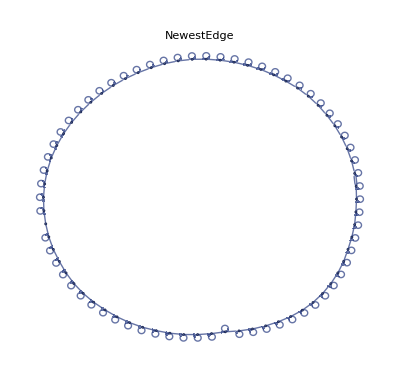
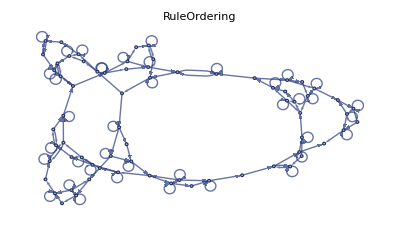
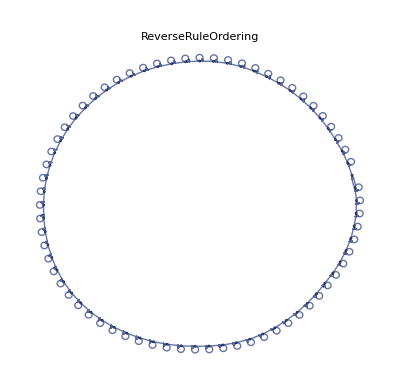

```mathematica
[{{{1,2},{2,3}}->{{4,4},{4,1},{2,4},{3,4}}},{{1,1},{1,1}},<|"MaxEvents"->68|>,"EventOrderingFunction"->{#,"LeastRecentEdge","RuleOrdering","RuleIndex"}]["FinalStatePlot",PlotLabel->#]&/@{"OldestEdge","LeastOldEdge","LeastRecentEdge","NewestEdge","RuleOrdering","ReverseRuleOrdering"}
```

## Graph Features of States

```mathematica
graph=[["FinalState"]];
```

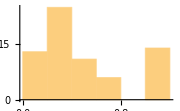

```mathematica
Histogram[ClosenessCentrality[graph],]
```

Cycle properties:

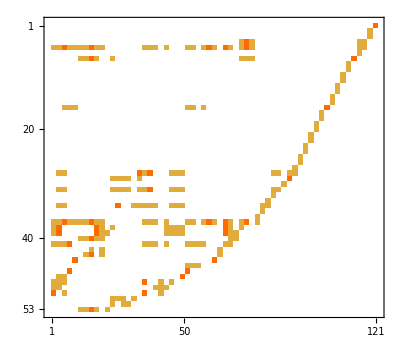

```mathematica
EdgeCycleMatrix[UndirectedGraph[graph]]//MatrixPlot
```

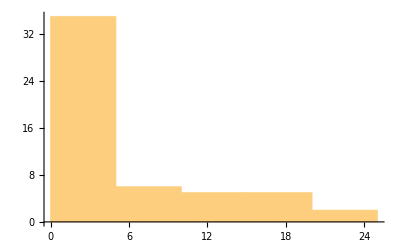

```mathematica
Histogram[Length/@FindFundamentalCycles[UndirectedGraph[graph]]]
```

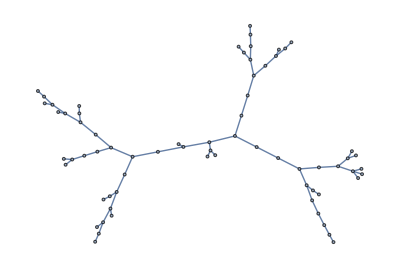

```mathematica
FindSpanningTree[UndirectedGraph[graph]]
```